-Graphics3D-

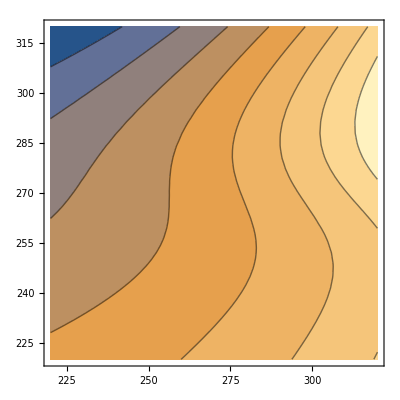

```mathematica
sigma = Quantity[5.67 *10^-8, "Watts"*("Meters"^-2)*("Kelvins"^-4)];
cp=Quantity[1000,"Joules"*("Kelvins"^-1)*("Kilograms"^-1)];
p=Quantity[10^5,"Pascals"];
g=Quantity[10,"Meters"*"Seconds"^-2];
c=(cp*p)/g;

tau = 0.68;

Plot3D[(1/c)(sigma*x^4(1-(0.45-0.25*Tanh[(y1-272)/23]))-(1/(1+tau))*sigma*y1^4),{x,220,320},{y1,220,320}]
ContourPlot[(1/c)(sigma*x^4(1-(0.45-0.25*Tanh[(y1-272)/23]))-(1/(1+tau))*sigma*y1^4),{x,220,320},{y1,220,320}]
```

#### Problem 1.b

```mathematica
a288=0.3
ts=Quantity[288, "Kelvins"]
tau2=0.68
Solve[t0^4(1-a288)==(1/(1+tau2))(ts^4),t0]
t0=((1/(1+tau2))*ts^4/(1-a288))^(1/4)
```

0.3

288 K

0.68

{{t0→-276.561 K},{t0→(0.-276.561 ⅈ) K},{t0→(0.+276.561 ⅈ) K},{t0→276.561 K}}

276.561 K

#### Problem 1.c

```mathematica
Solve[276.56082197998467^4(1-(0.45 -0.25*Tanh[(tsx-272)/23]))==(1/(1+tau2))(tsx^4),tsx]
```

Solve::inex: Solve was unable to solve the system with inexact coefficients or the system obtained by direct rationalization of inexact numbers present in the system. Since many of the methods used by Solve require exact input, providing Solve with an exact version of the system may help.

Solve[5.85009×10^9 (0.55+0.25 Tanh[1/23 (-272+tsx)])==0.595238 tsx^4,tsx]

#### Problem 2

```mathematica
ts2=270;
te=230;
N[Solve[ts2 == (1+tau2a)^(1/4)*te ,tau2a]]
tau2a=(ts2/te)^4-1.0
```

Solve::ivar: 0.899082 is not a valid variable.

Solve[True,0.899082]

0.899082

```mathematica
volcanoCO2 = Quantity[24*10^12, "Grams"]
```

24000000000000 g

```mathematica
Solve[0.8990819786950447*(4*10^-4)== 0.5 Log10[10*pCO2],pCO2]
ppCO2=Quantity[(1/10)(10^(2*tau2a)),"Bars"]
ppCO2now=Quantity[(1/10)(10^(2*tau2)),"Bars"]
ppCO2-ppCO2now
ppCO2pa=UnitConvert[ppCO2,"Pascals"]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{pCO2→0.100166}}

6.28296 bars

2.29087 bars

3.99209 bars

628296. Pa

```mathematica
rEarth= Quantity[6.4*10^6, "Meters"]
Solve[ppCO2pa==m*g/(4*Pi*rEarth^2),m]
m=UnitConvert[(4 * Pi*rEarth^2*ppCO2pa)/g,"Kilograms"]
```

6.4×10^6 m

{{m→3.23395×10^19 kg}}

3.23395×10^19 kg

```mathematica
flux=Quantity[24,"Teragrams"/"Years"]*(44/12)
```

88 Tg/yr

```mathematica
m/flux
```

3.67495×10^8 yr